```mathematica
(* A Monte Carlo simulation of gas breakdown between parallel plates *)
(* nc is the distance between plates, expressed as the number of collision lengths *)(* ni is the voltage, expressed as a multiple of the ionization voltage *)
(* reps is the number of electrons to toss *)
PaschenMcPlatesWeighted[nc_,ni_,reps_]:=Module[{results},
(* results will be a simple list of the ion counts produced by each electron *)
results=Table[
Module[{x0,x1,nIons,weight},
nIons=0;
x0=0;
weight=1;
(* This while loop is the Monte Carlo simulation *)
While[(x1=x0+RandomVariate[ExponentialDistribution[1]])≤nc,
(* If the electron has travelled far enough to gain enough energy
to ionize the molecule, then count an ion. *)
If[ni/nc(x1-x0)>1,nIons+=weight;weight*=2];
x0=x1;
];
nIons (* appends this count to the list of results *)
],{reps}];
(* Return the mean and error on the mean. *)
Around[Mean[results],StandardDeviation[results]/Sqrt[reps]]
]
```

## Banked Parallel Plate MC

```mathematica
(* A Monte Carlo simulation of gas breakdown between parallel plates *)
(* nc is the distance between plates, expressed as the number of collision lengths *)(* ni is the voltage, expressed as a multiple of the ionization voltage *)
(* reps is the number of electrons to toss *)
PaschenMcPlatesBanked[nc_,ni_,reps_]:=Module[{results,stack},
stack = CreateDataStructure["Stack"];
(* results will be a simple list of the ion counts produced by each electron *)
results=Table[
Module[{x0,x1,nIons},
nIons=0;
stack["Push",0];
While[!stack["EmptyQ"],
x0=stack["Pop"];
(* This while loop is the Monte Carlo simulation *)
While[(x1=x0+RandomVariate[ExponentialDistribution[1]])≤nc,
(* If the electron has travelled far enough to gain enough energy
to ionize the molecule, then count an ion, push the newly freed electron
onto the stack, and Sow the position where the ion was created. *)
If[ni/nc(x1-x0)>1,nIons++;stack["Push",x1];Sow[x1]];
x0=x1;
];
];
nIons (* appends this count to the list of results *)
],{reps}];
(* Return the mean and error on the mean. *)
Around[Mean[results],StandardDeviation[results]/Sqrt[reps]]
]
```

```mathematica
res20=Table[{ni,PaschenMcPlatesBanked[20,ni,100]},{ni,12,18}]
```

{{12,14.60.7},{13,21.51.1},{14,28.41.5},{15,41.52.2},{16,57.22.7},{17,78.23.4},{18,122.5.}}

```mathematica
r=Reap[PaschenMcPlatesBanked[20,15,20000]];r[[1]]
```

43.110.15

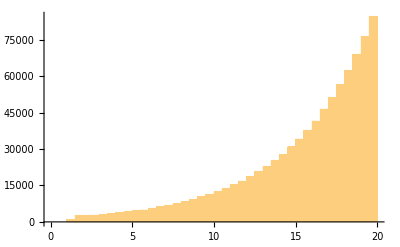

```mathematica
Histogram[r[[2,1]],{0,20,0.5}]
```

```mathematica
h=HistogramList[r[[2,1]],{0,20,0.5}]
```

{{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,20.},{0,0,851,2616,2678,2739,2980,3412,3777,4131,4547,4888,5563,6219,6803,7576,8319,9204,10282,11209,12503,13801,15246,16772,18699,20774,22845,25354,27668,30857,34101,37690,41527,46450,51096,56564,62386,69021,76396,84633}}

```mathematica
Total[h[[2]]]/20000//N
```

43.1089

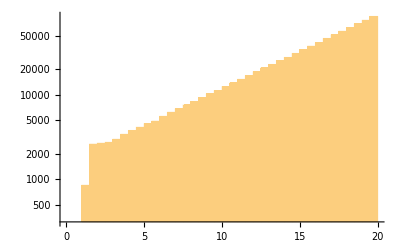

```mathematica
Histogram[r[[2,1]],{0,20,0.5},ScalingFunctions->{None,"Log"}]
```

```mathematica
Sqrt[851]//N
```

29.1719

```mathematica
Min[r[[2,1]]]
```

1.33336

```mathematica
λi=20/15; λi//N
```

1.33333

```mathematica
α=Exp[-λi];α//N
```

0.263597

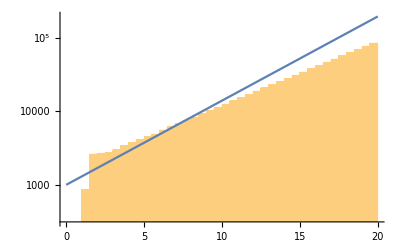

```mathematica
Show[Histogram[r[[2,1]],{0,20,0.5},ScalingFunctions->{None,"Log"}],
Plot[1000Exp[α x],{x,0,20},ScalingFunctions->{None,"Log"}]]
```

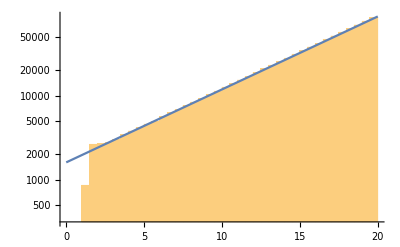

```mathematica
Module[{α,β},
α=0.2;
β=1600;
Show[Histogram[r[[2,1]],{0,20,0.5},ScalingFunctions->{None,"Log"}],
Plot[β Exp[α x],{x,0,20},ScalingFunctions->{None,"Log"}]]
]
```